```mathematica
(*---2. Count event-based starts (λ T logic)---*)
countStarts[times_,KK_,t_]:=Module[{n=Length[times]},Count[Table[If[i+KK-1<=n&&times[[i+KK-1]]-times[[i]]<=t,1,0],{i,1,n}],1]];

(*---3. Count clusters (scan logic,non-overlapping)---*)
countClusters[times_,KK_,t_]:=Module[{n=Length[times],i=1,count=0},While[i<=n-KK+1,If[times[[i+KK-1]]-times[[i]]<=t,(*Found a cluster*)count++;
(*Skip all events belonging to this cluster*)(*Move i forward until window breaks*)While[i<=n-KK+1&&times[[i+KK-1]]-times[[i]]<=t
,i++];
,i++]
];
count];

(*PARAMETERS*)
λ=1;
T=.;
KK=10;
A=2;
t=KK/A;
(*---1. Simulate Poisson process---*)
Simulate[T_]:=Module[{nEvents,times},
nEvents=RandomVariate[PoissonDistribution[λ T]];
times=Sort[RandomReal[{0,T},nEvents]];
{countStarts[times,KK,t]/T,
countClusters[times,KK,t]/T}];

(*---5. Output---*)
{"λ T Alerts (event-based)","ClusterAlerts (scan-based)"}->Simulate[3600]*3600
```

{λ T Alerts (event-based),ClusterAlerts (scan-based)}→{244,88}

```mathematica
g[Aλ_,KK_]:=Module[
{λ=1,A,t,nEvents,times},
A= Aλ*λ;
t=KK/A;
T=3600*1000;
nEvents=RandomVariate[PoissonDistribution[λ T]];
times=Sort[RandomReal[{0,T},nEvents]];
countClusters[times,KK,t]/(A T)];
nClusters[λ_,A_,KK_,T_]:=A T g[A/λ,KK];
```

```mathematica
estClusters[1,10, 10, 1000000]
estClusters[1*10, 10*10, 10, 1000000]/10.
```

2

0.8

```mathematica
estClusters[λ_,A_,KK_,T_]:=Module[
{t=KK/A,nEvents,times},
nEvents=RandomVariate[PoissonDistribution[λ T]];
times=Sort[RandomReal[{0,T},nEvents]];
countClusters[times,KK,t]]
```

```mathematica
estClusters[1,0.1,20,3600]
estClusters[1,0.9,20,3600]
estClusters[1,1.0,20,3600]
estClusters[1,1.0,20,3600]
estClusters[1,2.5,20,3600]
```

1

109

155

157

1

```mathematica
As=Range[1,11,0.1];
KK=5;
res=ParallelMap[g[#,KK]&,As];
KK->Round[res*1000000]/1000000.
KK=10;
res=ParallelMap[g[#,KK]&,As];
KK->Round[res*1000000]/1000000.

As14=Range[1,4,0.1];
KK=20;
res=ParallelMap[g[#,KK]&,As14];
KK->Round[res*1000000]/1000000.

As12=Range[1,2,0.1];
KK=50;
res=ParallelMap[g[#,KK]&,As12];
KK->Round[res*1000000]/1000000.
KK=100;
res=ParallelMap[g[#,KK]&,As12];
KK->Round[res*1000000]/1000000.
```

5→{0.082994,0.085757,0.084824,0.081208,0.076622,0.071227,0.065179,0.059155,0.053707,0.048457,0.043629,0.039236,0.035053,0.031524,0.0283,0.025409,0.022878,0.020471,0.018504,0.016591,0.014994,0.013521,0.012285,0.011061,0.010099,0.009126,0.008315,0.007563,0.00693,0.006288,0.005737,0.005307,0.004857,0.004429,0.0041,0.003801,0.003507,0.003198,0.002952,0.00276,0.002529,0.002362,0.002171,0.002037,0.001873,0.001751,0.001647,0.001523,0.001434,0.001335,0.001236,0.001158,0.001084,0.001011,0.000949,0.000903,0.000849,0.00079,0.000738,0.000706,0.000662,0.00062,0.000595,0.000557,0.000522,0.000493,0.00047,0.000437,0.000414,0.0004,0.000381,0.000357,0.000337,0.000324,0.000301,0.000294,0.000276,0.000266,0.000248,0.000243,0.000226,0.000222,0.000204,0.000201,0.000194,0.000179,0.00017,0.000162,0.00016,0.00015,0.000141,0.000135,0.000127,0.000126,0.000121,0.000111,0.00011,0.000109,0.000103,0.000097,0.000093}

10→{0.060881,0.061005,0.056953,0.050471,0.043253,0.035841,0.02942,0.023559,0.019052,0.015108,0.011937,0.009433,0.007484,0.005965,0.004719,0.003767,0.003,0.00237,0.001918,0.001538,0.001236,0.000994,0.000824,0.000666,0.000551,0.000452,0.000364,0.000303,0.000247,0.00021,0.000173,0.000146,0.000116,0.0001,0.000084,0.000071,0.00006,0.00005,0.000043,0.000038,0.000032,0.000027,0.000023,0.000019,0.000018,0.000013,0.000012,0.000012,0.000011,9.×10^-6,8.×10^-6,7.×10^-6,5.×10^-6,5.×10^-6,4.×10^-6,4.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

20→{0.043929,0.042027,0.03514,0.026362,0.018526,0.01257,0.008084,0.005246,0.003239,0.002026,0.001241,0.000751,0.000466,0.00029,0.000188,0.000108,0.000072,0.000045,0.00003,0.000018,0.000011,8.×10^-6,5.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.}

50→{0.027911,0.023777,0.013918,0.006484,0.002607,0.000928,0.00029,0.000107,0.000024,0.00001,2.×10^-6}

100→{0.019884,0.013535,0.004549,0.000987,0.000148,0.000017,1.×10^-6,0.,0.,0.,0.}

```mathematica
ToString[res]//Head
```

String

```mathematica
KK->ToString[Round[res*1000000]/1000000.]
```

5→{0.083133, 0.085851, 0.085067, 0.081598, 0.076915, 0.07095, 0.06528, 0.059286, 0.05381, 0.047744, 0.043633, 0.039116, 0.035381, 0.031705, 0.028505, 0.025368, 0.022465, 0.020352, 0.018462, 0.016355, 0.015011, 0.013588, 0.012384, 0.011097, 0.010136, 0.009042, 0.008395, 0.007474, 0.006888, 0.006358, 0.005634, 0.005282, 0.004805, 0.004426, 0.004185, 0.003849, 0.003517, 0.00328, 0.00291, 0.002707, 0.00256, 0.002339, 0.002192, 0.001976, 0.001821, 0.00174, 0.001642, 0.001586, 0.001431, 0.001375, 0.001228, 0.001185, 0.001105, 0.001018, 0.000932, 0.0009, 0.000804, 0.000789, 0.000721, 0.000692, 0.000689, 0.000652, 0.000557, 0.000551, 0.000527, 0.000501, 0.000453, 0.000434, 0.00041, 0.000403, 0.000385, 0.000361, 0.000338, 0.000327, 0.000319, 0.000274, 0.000269, 0.000278, 0.000251, 0.000237, 0.000236, 0.000211, 0.000216, 0.000203, 0.00019, 0.000186, 0.000172, 0.000151, 0.00015, 0.000151, 0.000144, 0.000142, 0.000136, 0.000129, 0.000131, 0.000107, 0.000111, 0.000107, 0.000096, 0.000104, 0.000095}

```mathematica
As=Range[1,10,0.1];
res=ParallelMap[g[#,10]&,As];
res2=ParallelMap[g[#,20]&,As];
```

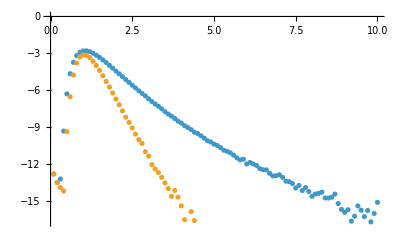

```mathematica
ListPlot[{Transpose[{As,Log@res}],Transpose[{As,Log@res2}]}]
```

```mathematica
KK=5
As=Range[1,10,0.1];
res=ParallelMap[g[#,KK]&,As];
Round[Log[res]100]/100//N
```

5

$Aborted

{-2.8,-2.79,-2.86,-2.98,-3.14,-3.33,-3.53,-3.74,-3.96,-4.19,-4.43,-4.66,-4.89,-5.13,-5.36,-5.59,-5.81,-6.04,-6.26,-6.48,-6.69,-6.9,-7.11,-7.32,-7.52,-7.72,-7.92,-8.11,-8.29,-8.48,-8.66,-8.86,-9.04,-9.21,-9.39,-9.55,-9.72,-9.88,-10.06,-10.2,-10.36,-10.51,-10.68,-10.81,-10.98,-11.09,-11.24,-11.42,-11.58,-11.76,-11.82,-11.9,-12.1,-12.19,-12.31,-12.52,-12.59,-12.8,-12.88,-12.96,-13.09,-13.23,-13.28,-13.44,-13.48,-13.73,-13.79,-13.94,-14.09,-14.04,-14.21,-14.47,-14.4,-14.66,-14.72,-14.66,-15.06,-14.84,-14.86,-15.12,-15.23,-15.36,-15.36,-15.66,-15.67,-15.8,-15.88,-15.89,-15.99,-16.26,-16.37}

```mathematica
As=Range[1,10,0.1];
res=ParallelMap[g[#,10]&,As];
Round[Log[res]100]/100//N
```

{-2.8,-2.79,-2.86,-2.98,-3.14,-3.33,-3.53,-3.74,-3.96,-4.19,-4.43,-4.66,-4.89,-5.13,-5.36,-5.59,-5.81,-6.04,-6.26,-6.48,-6.69,-6.9,-7.11,-7.32,-7.52,-7.72,-7.92,-8.11,-8.29,-8.48,-8.66,-8.86,-9.04,-9.21,-9.39,-9.55,-9.72,-9.88,-10.06,-10.2,-10.36,-10.51,-10.68,-10.81,-10.98,-11.09,-11.24,-11.42,-11.58,-11.76,-11.82,-11.9,-12.1,-12.19,-12.31,-12.52,-12.59,-12.8,-12.88,-12.96,-13.09,-13.23,-13.28,-13.44,-13.48,-13.73,-13.79,-13.94,-14.09,-14.04,-14.21,-14.47,-14.4,-14.66,-14.72,-14.66,-15.06,-14.84,-14.86,-15.12,-15.23,-15.36,-15.36,-15.66,-15.67,-15.8,-15.88,-15.89,-15.99,-16.26,-16.37}

```mathematica
Round[Log[res]100]/100//N
```

{-2.8,-2.79,-2.86,-2.98,-3.15,-3.32,-3.53,-3.75,-3.96,-4.2,-4.43,-4.66,-4.89,-5.12,-5.36,-5.58,-5.82,-6.04,-6.26,-6.49,-6.69,-6.89,-7.12,-7.31,-7.52,-7.71,-7.93,-8.13,-8.29,-8.46,-8.66,-8.86,-9.01,-9.19,-9.34,-9.51,-9.71,-9.88,-10.02,-10.18,-10.36,-10.54,-10.56,-10.78,-10.94,-11.16,-11.28,-11.45,-11.54,-11.63,-11.79,-12.04,-12.01,-12.12,-12.35,-12.44,-12.55,-12.87,-12.97,-12.72,-13.02,-13.11,-13.1,-13.47,-13.43,-13.71,-13.95,-13.88,-13.97,-14.03,-14.23,-14.24,-14.2,-14.44,-14.74,-14.19,-14.95,-15.47,-15.07,-14.51,-15.21,-15.,-16.22,-15.25,-15.26,-15.27,-15.57,-15.76,-16.69,-16.29,-17.4}

```mathematica
3600 As res
%-3600 As Exp[Round[Log[res]100]/100]
```

{219.723,242.742,246.62,237.298,216.801,194.458,169.327,144.624,123.42,102.787,85.76,71.587,59.43,49.365,40.545,33.815,27.849,23.126,19.286,15.901,13.386,11.36,9.283,7.923,6.613,5.663,4.68,3.933,3.441,2.965,2.501,2.088,1.847,1.577,1.386,1.201,1.007,0.864,0.766,0.672,0.572,0.485,0.486,0.397,0.344,0.282,0.254,0.218,0.204,0.189,0.164,0.13,0.136,0.124,0.1,0.093,0.084,0.062,0.057,0.074,0.056,0.052,0.053,0.037,0.039,0.03,0.024,0.026,0.024,0.023,0.019,0.019,0.02,0.016,0.012,0.021,0.01,0.006,0.009,0.016,0.008,0.01,0.003,0.008,0.008,0.008,0.006,0.005,0.002,0.003,0.001}

{0.806775,-0.486007,-0.781044,-0.412462,0.826281,-0.767291,0.530685,0.695395,-0.108981,0.217255,-0.0243256,0.0205442,-0.139666,-0.11647,-0.0708288,-0.13809,0.0722158,-0.0227526,0.0206424,0.0473484,-0.0414539,0.0000815345,-0.033993,-0.0225466,-0.0227026,0.0141494,0.0171681,0.00935157,0.00712215,-0.00827987,0.00426598,-0.00725675,-0.000389663,-0.00280931,-0.00537667,0.000465924,0.00224329,-0.00210566,-0.00297643,0.00306987,0.00185979,-0.000745558,0.000537022,-0.0000853417,-0.000758219,0.000201438,-0.000477138,-0.000527219,0.000777321,0.0000661877,0.000272433,0.000363656,0.000225734,0.000406984,0.000242485,0.000403941,-0.000226875,-0.0000879501,-0.0000180005,-0.000289217,0.000167588,0.000244061,-0.0000123778,-0.000126045,-0.000170519,-4.50161×10^-6,0.0000829247,0.0000112245,-0.0000604193,0.0000502473,-0.0000275123,-0.0000736627,-0.0000971609,-1.77923×10^-6,2.76617×10^-6,-0.0000417922,0.0000436891,0.0000119403,-0.000035815,1.4886×10^-6,-0.0000338911,-0.00002136,8.88004×10^-6,0.0000238264,0.0000182787,0.0000136311,0.000021274,4.33624×10^-6,8.62214×10^-6,-1.10082×10^-6,9.70033×10^-7}

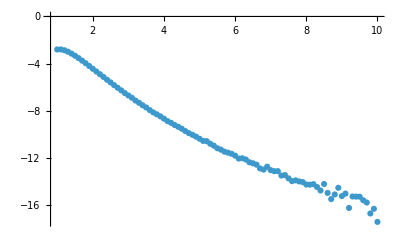

```mathematica
ListPlot[Transpose[{ts,Log[res]}],PlotRange->Full]
```

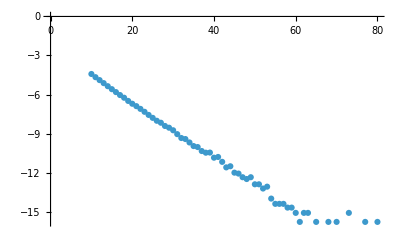

```mathematica
ns=Range[10,100,1];
res2=ParallelMap[g[2,#]&,ns];
ListPlot[Transpose[{ns,Log@res2}]]
```

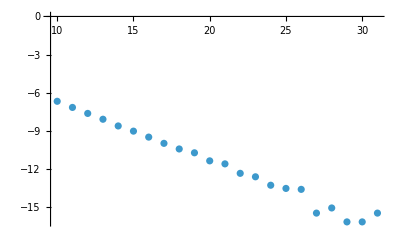

```mathematica
ns=Range[10,100,1];
res2=ParallelMap[g[3,#]&,ns];
ListPlot[Transpose[{ns,Log@res2}]]
```

```mathematica
8450*3
```

25350

```mathematica
Simulate[360000]
```

{12007/180000,4189/180000}

```mathematica
Total[ParallelTable[Simulate[],100]]/100.
Total[ParallelTable[Simulate[],100]]/100.
Total[ParallelTable[Simulate[],100]]/100.
```

{249.17,88.18}

{245.5,85.09}

{239.83,85.37}

```mathematica
{λ,A,T,KK}
```

{1,2,3600,10}

```mathematica
(λ T)(1-Exp[-(λ KK)/A]Sum[((λ KK)/A)^n/n!,{n,0,KK-1}])//N

(A T-KK)(1-Exp[-(λ KK)/A]Sum[((λ KK)/A)^n/n!,{n,0,KK-1}])//N
```

114.581

228.844

```mathematica
1/Exp[-(λ KK)/A]//N
```

6.05668169507×10^3365

```mathematica
Sum[((λ KK)/A)^n/(n!),{n,0,KK-1}]//N
```

2.78264×10^29

```mathematica
λ T
A T-KK
```

3600

7190

```mathematica
3.464+0.069+0.070+0.874+0.257+0.214+1.354
```

6.302

```mathematica
0.566+2.420+0.277+0.024
```

3.287

```mathematica
0.016+0.047+0.544
```

0.607

```mathematica
0.3
```

```mathematica
0.11+0.16+0.55+0.028+0.029+0.043+0.024
```

0.944

```mathematica
0.121+0.145+0.069+0.057+0.259
```

0.651

```mathematica
0.94+0.6+0.65
```

2.19